MessageName::messg: RxnsysToSrxnsys::usage cannot be set to  Produces reactions in srxn[[reaction index],{x1,x2},{x3},k] format ( ). Removes any other statements.   reaction index is 1-based reaction structured system. It must be set to a string.

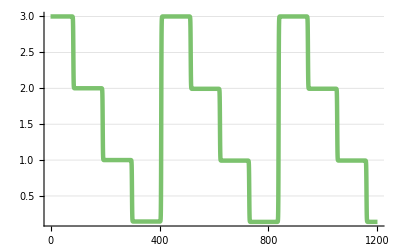

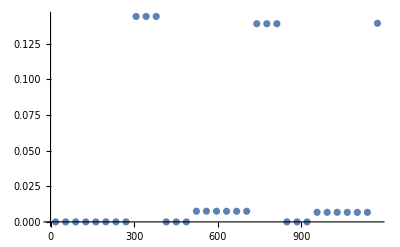

maximum error for c: 0.144032

```mathematica
Get[ParentDirectory[NotebookDirectory[]]<>"/packages/init.m"]
Get[NotebookDirectory[]<>"/counter.m"]
rsys=CounterRsys[3];
tmax=1200;
sol=SimulateRxnsys[ExpandDiscreteRsys[rsys],tmax];
PlotForPaper[{c[t]}/.sol,tmax,200]
errorMap=EvaluateError[rsys, tmax];
cErrorList=errorMap[c]/.{resultMap_}:>{resultMap["time"],resultMap["error"]};
ListPlot[cErrorList,Ticks->{Range[0,tmax,100],Automatic}]
Print["maximum error for c: "<>ToString[Max[cErrorList/.{time_,error_}->error]]];
```